# Tracking junctions and their angles over time

Here we analyze the coarsening process in the asymmetric 3-species McRD system with mutual detachment.

Using measurements from notebook “3sMutualDetachment-tuningDm-genGibbsThomsonRel-pub-v2.nb” for Dm1/Dm2 = Dm1/Dm3 = 10^1.3 ~ 20 for effective interfacial tensions and core turnover.
The core turnover vector is rotated such that it applies to a junction with the BC (23) interface aligned with the x axis.

```mathematica
σInt={0.25305862853589955,0.25305862853589955,0.13920100927170612};
tCore=RotationMatrix[0.01481643186044432].({0.00384502487544963,-0.003638048485286391}-{-0.036899604862661375,-0.0003773182251293394});
tCore
```

{0.0407885,-0.0026567}

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

### Find junctions and extract data for each data

```mathematica
ClearAll@findBranchPoints;
Options[findBranchPoints]={"dataRadius"->5};
findBranchPoints[dataInt_,opts:OptionsPattern[]]:=Block[{
branchPoints=MorphologicalBranchPoints[Pruning[Thinning[Binarize[ImageAdjust@ImageReflect@Image[dataInt],0.1]],2]],
branchPointCoords,
bpcSel,
dy=Length[dataInt]
},
branchPointCoords=PixelValuePositions[branchPoints,1];
bpcSel=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords,0]]}]/@branchPointCoords,#[[-1]]>OptionValue["dataRadius"]&];(*minimal distance from other branch points*)
bpcSel
];
```

```mathematica
ClearAll@dataJunctions;
Options[dataJunctions]={"dataRadius"->15};
dataJunctions[dataInt_,dataA_,dataB_,dataC_,opts:OptionsPattern[]]:=Block[{
interfaces,
branchPoints,
bpData,
gDataB=(ImageData@GradientFilter[Image[dataB],1])^2,
gDataC=(ImageData@GradientFilter[Image[dataC],1])^2,
maxDens=Map[Which[#[[1]]>#[[2]]&&#[[1]]>#[[3]],{1,0,0},#[[2]]>#[[1]]&&#[[2]]>#[[3]],{0,1,0},#[[3]]>#[[1]]&&#[[3]]>#[[2]],{0,0,1}]&,Transpose[{dataA,dataB,dataC},{3,1,2}],{2}],
dx,dy,
r=OptionValue["dataRadius"]
},
interfaces=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataInt,gDataB,gDataC,maxDens},{3,1,2}];
{dy,dx}=Dimensions[dataInt][[;;2]];
branchPoints=findBranchPoints[dataInt(*,opts*)];
bpData=Table[
{
junction[[1]],
{#[[1]]-junction[[1,1]],#[[2]]-junction[[1,2]],Sequence@@#[[3;;]]}&/@Select[
Flatten[
interfaces[[Max[1,Floor[junction[[1,2]]-r-1]];;Min[dy,Ceiling[junction[[1,2]]+r+1]],Max[1,Floor[junction[[1,1]]-15]];;Min[dx,Ceiling[junction[[1,1]]+r+1]]]],
1],
(Norm[junction[[1]]-#[[{1,2}]]]<Min[r,junction[[2]]])&]
},
{junction,branchPoints}];

bpData
];
```

### Functions for fitting junctions

#### Cross-section of the gradients at the interfaces

Use the interface analysis of single junctions in “3sMutualDetachment-tuningDm-genGibbsThomsonRel-pub-v2.nb” to determine the profiles of Σ_i D_m,i |\nabla rho_i|^2 at the single interfaces.

```mathematica
NotebookEvaluate[ParentDirectory[NotebookDirectory[]]<>"/3sMutualDetachment-tuningDm-genGibbsThomsonRel-pub-v2.nb",
InsertResults->False,
EvaluationElements->"InitializationCell"
];
```

```mathematica
ClearAll@intCrossSec;
intCrossSec[angles_,dataσ_,grid_]:=Block[{
measurementPoints,
tvecBC,
nvecBC,
tvecAC,
nvecAC,
tvecAB,
nvecAB,
xyData,
dataAC,
dataAB,
dataBC,
dataABAC,
BCDomainCorners,
boundaryDist,
junctionDist,
dx=Abs[grid[[1,2,1]]-grid[[1,1,1]]],
L=Max[grid[[1,All,1]]]+Abs[grid[[1,2,1]]-grid[[1,1,1]]]/2
},
(*determine geometry of rectangles intersecting interface perpendicularly which are used to measure the effective interfacial tension*)
measurementPoints=evalPoints[angles,L];
tvecBC=measurementPoints[[1,2]];
nvecBC={-#[[2]],#[[1]]}&@measurementPoints[[1,2]];
tvecAC=measurementPoints[[2,2]];
nvecAC={#[[2]],-#[[1]]}&@measurementPoints[[2,2]];
tvecAB=measurementPoints[[3,2]];
nvecAB={#[[2]],-#[[1]]}&@measurementPoints[[3,2]];

xyData=Transpose[{grid[[All,All,1]],grid[[All,All,2]],dataσ},{3,1,2}];
dataAC={nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]]),#[[3]]}&/@Select[Flatten[xyData[[Floor[Length[xyData]/2];;]](*These restrictions to certain parts of the data are made to make the selection faster. Needs to be changed depending on where the junction is positioned within the data.*),1],((Abs[tvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<2)&&(Abs[nvecAC.(#[[{1,2}]]-measurementPoints[[2,1]])]<1.5))&];

dataAB={nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]]),#[[3]]}&/@Select[Flatten[xyData[[;;Floor[Length[xyData]/2]]],1],((Abs[tvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<2)&&(Abs[nvecAB.(#[[{1,2}]]-measurementPoints[[3,1]])]<1.5))&];
(*sum the data for the interfaces which are the same type due to symmetry*)
dataABAC=Join[dataAC,dataAB];

BCDomainCorners={#+1.5nvecBC,#-1.5nvecBC}&@measurementPoints[[1,1]]+2tvecBC;
boundaryDist=dist/.FindRoot[Max[Norm/@(BCDomainCorners+dist tvecBC)]==L,{dist,0}];
(*ensure that the edge of the measurement region is at least 1 distant from the junction*)
junctionDist=Norm[measurementPoints[[1,1]]-(xJunc/.angles[[3]])]-2;
If[junctionDist>1,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],((Abs[tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<2)&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];,
If[boundaryDist>0,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<2)&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];,
dataBC={nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]),#[[3]]}&/@Select[Flatten[xyData[[All,Floor[Length[xyData[[1]]]/2];;]],1],(((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))<(2+boundaryDist))&&((tvecBC.(#[[{1,2}]]-measurementPoints[[1,1]]))>-(2+junctionDist-1))&&(Abs[nvecBC.(#[[{1,2}]]-measurementPoints[[1,1]])]<1.5))&];
]
];
Print[
ListPlot[{dataABAC,dataBC},PlotRange->All]
];
{dataABAC,dataBC}
];
```

Fit a piecewise linear model with grid spacing dx to the interface profiles.
Use least-squares regression in which case fitting corresponds to solving a linear system of equations for the values of the model at the grid points.

```mathematica
ClearAll@pwlModel;
pwlModel[xydata_,dxσ_]:=Block[{
minx=Min[xydata[[All,1]]],
maxx=Max[xydata[[All,1]]],
elementCoords,
elements,
eldata,
overlap,
intMat,
pwlCoords,
pwlF
},
(*fit*)
elementCoords=Range[minx,maxx,dxσ];
elements=UnitTriangle[(x-#)/dxσ]&/@elementCoords;(*summing those elements up with amplitudes {a_i} gives a piecewise-linear function connecting the points {(elementCoords_i,a_i)}*)
eldata=elements/.x->xydata[[All,1]];
overlap=(xydata[[All,2]].#)&/@eldata;
intMat=Outer[Dot,eldata,eldata,1];
pwlCoords=LinearSolve[intMat,overlap];

(*resulting piecewise-linear function*)
pwlF[x_]:=Piecewise[Join[{{0,x<elementCoords[[1]]-dxσ}},{InterpolatingPolynomial[#,x],x<#[[2,1]]}&/@Partition[Transpose[{elementCoords,pwlCoords}],2,1]]];
(*return compiled function*)
Compile[{{x,_Real}},
Evaluate[N[pwlF[x]]],
RuntimeAttributes->{Listable}
]
];
```

#### Loss function for fitting

First, fit the interfaces roughly, not considering their profile.

```mathematica
ClearAll@fitDomains;
fitDomains=Compile[{{ang1,_Real},{ang2,_Real},{pnts,_Real,2},{w,_Real}},
Block[{
angS1,
angS2,
modelA,
modelB,
modelC,
model
},
(*case that ang1<ang2, domains are sorted as A, C, B in positive angular direction*)
{angS1,angS2}=Sort[{ang1,ang2}];
modelA=Function[pnt,{1,0,0}((1+Tanh[Mod[pnt[[1]],2Pi,angS2-2Pi]pnt[[2]]/w])/2)((1+Tanh[(angS1-Mod[pnt[[1]],2Pi,angS2-2Pi])pnt[[2]]/w])/2)]/@pnts;
modelB=Function[pnt,{0,1,0}((1+Tanh[(Mod[pnt[[1]],2Pi,angS1]-angS2)pnt[[2]]/w])/2)((1+Tanh[(2Pi-Mod[pnt[[1]],2Pi,angS1])pnt[[2]]/w])/2)]/@pnts;
modelC=Function[pnt,{0,0,1}((1+Tanh[(Mod[pnt[[1]],2Pi]-angS1)pnt[[2]]/w])/2)((1+Tanh[(angS2-Mod[pnt[[1]],2Pi])pnt[[2]]/w])/2)]/@pnts;
model=modelA+modelB+modelC;
(*if the orientation of the junction is the other way around (B,C,A), we have*)
If[ang1>ang2,
model=({{0,1,0},{1,0,0},{0,0,1}}.#)&/@model;
];

Total[Norm[#[[1]]-#[[2]]]^2&/@Transpose[{pnts[[All,{3,4,5}]],model}]]
],
CompilationTarget->"C"
];
```

```mathematica
ClearAll@lossFdomains;
Options[lossFdomains]={"width"->1};
(*angles ordered as AB,AC,BC*)
lossFdomains[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ,opts:OptionsPattern[]]:=
Block[{
data=Select[{PlanarAngle[{x1,x2}->{{x1,x2}+{Cos[angles[[1]]],Sin[angles[[1]]]},#[[;;2]]}],Norm[{x1,x2}-#[[;;2]]],Sequence@@#[[-1]]}&/@vertexData,VectorQ],
angs=PlanarAngle[{0,0}->{{Cos[angles[[1]]],Sin[angles[[1]]]},{Cos[#],Sin[#]}}]&/@angles[[2;;]]
},

fitDomains[angs[[1]],angs[[2]],data,OptionValue["width"]]
];
```

Second, fit the interface profiles to find the angles reliably:

Use the symmetry B<->C in the system (given the parameters chosen) such that the BC interface is symmetric and the AB and AC interfaces have the same profiles.
pwlmBC & pwlmABAC (oriented such that spatial axis points towards the A domain) first have to be calculated in the analysis section below.
The interface angles are ordered such that they correspond to the interfaces AB,AC,BC.
xScale accounts for changes in the spatial scale of the resolution of the data between the interface profile and the data fitted.

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,xScale_?NumericQ,amp_?NumericQ,angles_?VectorQ]:=
Block[{
angleABAC=Mod[angles[[2]]-angles[[1]],2Pi],
angleABBC=Mod[angles[[3]]-angles[[1]],2Pi],
orient,
anglesLabeled=Transpose[{Range[3],angles}],
loss
},
(*as AB and AC interfaces can be asymmetric, need to find out their orientation*)
orient=If[angleABAC>angleABBC,(*in mathematically positive direction, the AB interface separates A from B*)
1,
-1];

loss=
Function[d,
{(1+Tanh[#[[4]]-3])/2,(d[[3]]-amp  Which[#[[3]]==1,pwlmABAC[xScale*#[[2]]],#[[3]]==2,pwlmABAC[-xScale*#[[2]]],#[[3]]==3,pwlmBC[xScale*#[[2]]]])^2}(*weight and square loss from interface model*)
&@First[SortBy[If[Length@#==0,{{1000,1000,1,1000}},#],First](*choose interface clostest to point*)
&@({Norm[(d[[{1,2}]]-{x1,x2}).{Sin[#[[2]]],-Cos[#[[2]]]}],orient(d[[{1,2}]]-{x1,x2}).{Sin[#[[2]]],-Cos[#[[2]]]},#[[1]],(d[[{1,2}]]-{x1,x2}).{Cos[#[[2]]],Sin[#[[2]]]}}(*measure distance of point from each interface*)
&/@
Select[anglesLabeled,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle[[2]]],Sin[angle[[2]]]})>-10^-10](*for each point in vertexData, choose interfaces it could belong to*)
])
]]/@vertexData;

loss[[All,1]].loss[[All,2]]/Total[loss[[All,1]]](*normalize weights*)
];
```

#### Fitting functions

These functions use the loss function defined above to fit the junctions in the data.

```mathematica
ClearAll@measureJunction;
(*Here, each entry in vertexData[[2]] is (x, y, gradDataB, gradDataC); this function only measures triple junctions*)
measureJunction[vertexData_]:=
Block[
{
dataW,
iniCondB,
iniCondC,
iniCondCleanB,
iniCondCleanC,
angDist,
iniCond,
vars,
solIni,
sol,sol2,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
(*once for the gradient data of the B field*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[4]]}&/@vertexData[[2]]);
iniCondB=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.2+(HistogramList[dataW,{0,2Pi,0.4}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.4}],0.5,0,1,Padding->"Periodic"]));
(*Print[Histogram[dataW,{0,2Pi,0.4}]];*)
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondCleanB=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCondB,{#[[1]]-2Pi,#[[2]]}&/@iniCondB,{#[[1]]+2Pi,#[[2]]}&/@iniCondB],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCondB}],#[[2]]&][[All,1]];

(*once for the gradient data of the C field*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[5]]}&/@vertexData[[2]]);
iniCondC=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.2+(HistogramList[dataW,{0,2Pi,0.4}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.4}],0.5,0,1,Padding->"Periodic"]));
(*Print[Histogram[dataW,{0,2Pi,0.4}]];*)
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondCleanC=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCondC,{#[[1]]-2Pi,#[[2]]}&/@iniCondC,{#[[1]]+2Pi,#[[2]]}&/@iniCondC],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCondC}],#[[2]]&][[All,1]];

(*check that we found a triple junction*)
If[(Length[iniCondCleanB]!=2)||(Length[iniCondCleanC]!=2),
sol=I,

(*identify which of the interfaces in iniCondCleanB and -C are the same*)
angDist={Min[#],SortBy[Transpose[{Range[Length@#],#}],Last][[All,1]]}(*find minimal distance and index for which angle it occurs*)
&/@Outer[Min[{#,2Pi-#}&@Abs[#1-#2]]&,iniCondCleanB,iniCondCleanC];(*determine angle differences between all angles; one row in angDist corresponds to the angular distances of one angle measured in B data two the angles measured in the C data*)

If[angDist[[1,1]]<angDist[[2,1]],(*if first B angle is closer to C angles than the second B angle*)
iniCond={
iniCondCleanB[[2]],
iniCondCleanC[[angDist[[1,2,2]]]],
If[Abs[iniCondCleanB[[1]]-#]<Pi/2,#,Mod[#-Pi,2Pi,-Pi]](*ensure the mean was calculated the right way around the circle*)
&@Mean[{iniCondCleanB[[1]],iniCondCleanC[[angDist[[1,2,1]]]]}]
};(*order it as AB,AC,BC*),
iniCond={iniCondCleanB[[1]],iniCondCleanC[[angDist[[2,2,2]]]],If[Abs[iniCondCleanB[[2]]-#]<Pi/2,#,Mod[#-Pi,2Pi,-Pi]](*ensure the mean was calculated the right way around the circle*)
&@Mean[{iniCondCleanB[[2]],iniCondCleanC[[angDist[[2,2,1]]]]}]};(*order it as AB,AC,BC*)
];

(*fit junction*)
vars=Symbol["a"<>ToString[#]]&/@Range[3];

(*first rough fit based on the A, B, C domains*)
solIni=Quiet@Check[Last@FindMinimum[lossFdomains[vertexData[[2]],x1,x2,vars,"width"->1],Join[{{x1,0.1,-10,10},{x2,0.1,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[3]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];

(*fit the detailed interface profile*)
If[solIni===I,
sol=Quiet@Check[Last@FindMinimum[lossF[vertexData[[2]],x1,x2,0.1,1.,vars],Join[{{x1,0.,-10,10},{x2,0.,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[3]],AccuracyGoal->2,PrecisionGoal->2,Method->"Newton"],I];,
sol=Quiet@Check[Last@FindMinimum[lossF[vertexData[[2]],x1,x2,0.1,1.,vars],Join[{{x1,x1/.solIni,-10,10},{x2,x2/.solIni,-10,10}},{vars[[#]],vars[[#]]/.solIni,-2Pi,2Pi}&/@Range[3]],AccuracyGoal->2,PrecisionGoal->2,Method->"Newton"],I];
];
];

(*check that all angles fit a different arm, asking that all angles are > 10˚*)
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)];(*angles are ordered according to the interface they describe: AB, AC, BC*)
If[Min[Abs@Differences[Sort[fit[[2;;]]]]]<10/180Pi,
I,
fit]
]
(*return I if the fit as a triple junction didn't succeed*)
];
```

```mathematica
ClearAll@measureJunctions;
Options[measureJunctions]=Options[dataJunctions];
(*measure all triple junctions in a single frame of the data*)
measureJunctions[dataInt_,dataA_,dataB_,dataC_,opts:OptionsPattern[]]:=
Block[
{
bpData
},
bpData=dataJunctions[dataInt,dataA,dataB,dataC,opts];
Select[ParallelTable[measureJunction[bpdata],{bpdata,bpData},Method->"FinestGrained"],#=!=I&]
];
```

## Import data

```mathematica
dataDensities=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-asymmDm-coarsening-ensembleSize3.txt","Comsol2DSweep"];
```

```mathematica
times=dataDensities["Times"]/.E5->10^5;
```

```mathematica
indIni=102;
tIni=times[[indIni]] (*time from which on interfaces have formed*)
```

100

```mathematica
dataA=dataDensities["m1+c1"];
dataB=dataDensities["m2+c2"];
dataC=dataDensities["m3+c3"];
```

```mathematica
dataGrads=Import[NotebookDirectory[]<>"mutualDetachment-Dc_1-asymmDm-coarsening-grads-ensembleSize3.txt","Comsol2DSweep"];
```

```mathematica
dataInt=dataGrads["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"];
```

Measure space in pixels

```mathematica
grid=Table[{j,i},{i,1,Dimensions[dataInt[[1]]][[1]]},{j,1,Dimensions[dataInt[[1]]][[2]]}];
```

## Data visualization

```mathematica
Manipulate[Image[dataInt[[Floor@i]]]//ImageAdjust,{{i,52},1,Length@dataInt}]
```

```mathematica
Image[dataInt[[indIni]]]//ImageAdjust//ImageReflect
```

## Junction analysis

### Find interface cross sections

Field that, integrated across an interface, gives σ. Used in 3sPAR-mutualDetachment-tuningDm-measureNeumannAngle-pub-final.nb

```mathematica
dataST=Import[ParentDirectory[NotebookDirectory[]]<>"/mutualDetachment-Dc_1-NeumannAngles-surfaceTension-fine0_05.txt","Comsol2DSweep"];
```

```mathematica
dataσ=dataST["Dm1*((m1x+c1x)^2+(m1y+c1y)^2)+Dm2*((m2x+c2x)^2+(m2y+c2y)^2)+Dm3*((m3x+c3x)^2+(m3y+c3y)^2)"][[14]];
```

```mathematica
gridσ=dataST["Grid"];
```

Fit of the single junction obtained in 3sPAR-mutualDetachment-tuningDm-measureNeumannAngle-pub-final.nb

```mathematica
anglesσ={19.953,2.778764911758132,{xJunc->{-1.87653336110319,0.029342624333127412},dInt->0.04229053654953643,R->53.93685152005031,phiCircleB->3.3230065245056237,phiLin->-0.01481643186044432}};
```

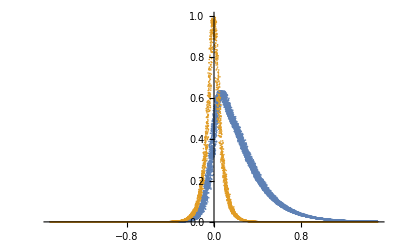

```mathematica
crossSecData=intCrossSec[anglesσ,dataσ,gridσ];
```

Piecewise linear model

```mathematica
pwlmABAC=pwlModel[crossSecData[[1]],0.02];
pwlmBC=pwlModel[crossSecData[[2]],0.02];
```

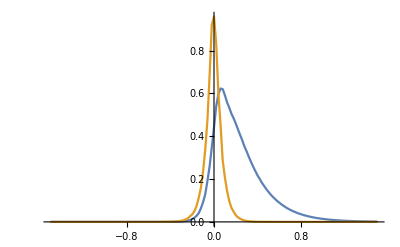

```mathematica
ListPlot[{
{#,pwlmABAC[#]}&/@Range[-1.5,1.5,0.02],
{#,pwlmBC[#]}&/@Range[-1.5,1.5,0.02]
},PlotRange->All,Joined->True]
```

### Example of junction fitting

```mathematica
bpdataTest=dataJunctions[dataInt[[102]],dataA[[102]],dataB[[102]],dataC[[102]],"dataRadius"->10];
```

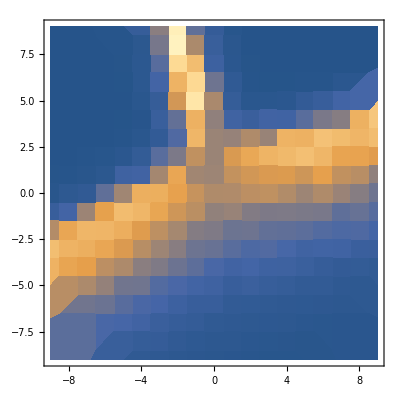

```mathematica
ListDensityPlot[{
{#[[1]],#[[2]],#[[3]]}&/@bpdataTest[[2,2]]
},PlotRange->All,AspectRatio->1,InterpolationOrder->0]
```

```mathematica
measureJunction[bpdataTest[[2]]]
```

{73.7175,283.12,0.22558,-2.66115,1.8296}

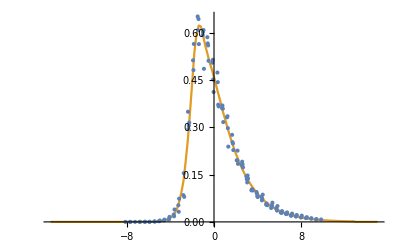

```mathematica
ListPlot[{
{{-Sin[-2.6611463999430196],Cos[-2.6611463999430196]}.{#[[1]],#[[2]]},#[[3]]}&/@Select[bpdataTest[[2,2]],-#[[1]]-#[[2]]>1&],
{# 10,pwlmABAC[(#+0.2)]}&/@Range[-1.5,1.5,0.02]
},PlotRange->All,Joined->{False, True}]
```

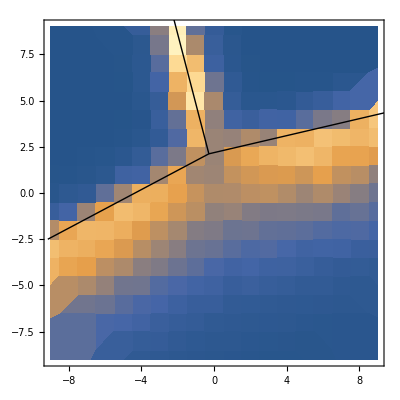

```mathematica
Show[
ListDensityPlot[{
{#[[1]],#[[2]],#[[3]]}&/@bpdataTest[[2,2]]
},PlotRange->All,AspectRatio->1,InterpolationOrder->0],
Graphics[Join[{Black,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+10{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@{{73.71751005953641,283.1199632716092,0.2255801673575122,-2.6611463999430196,1.8296013801630366}-{bpdataTest[[2,1,1]],bpdataTest[[2,1,2]],0,0,0}},1]]]
]
```

### Junction analysis

```mathematica
Monitor[frameJunctions[sim->1]=Table[
measureJunctions[dataInt[[i]],dataA[[i]],dataB[[i]],dataC[[i]],"dataRadius"->10],
{i,indIni,Length[times]}];,i]
```

```mathematica
Export[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-1.txt",frameJunctions[sim->1]]
```

```mathematica
Monitor[frameJunctions[sim->2]=Table[
measureJunctions[dataInt[[Length[times]+i]],dataA[[Length[times]+i]],dataB[[Length[times]+i]],dataC[[Length[times]+i]],"dataRadius"->10],
{i,indIni,Length[times]}];,i]
```

```mathematica
Export[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-2.txt",frameJunctions[sim->2]]
```

```mathematica
Monitor[frameJunctions[sim->3]=Table[
measureJunctions[dataInt[[2Length[times]+i]],dataA[[2Length[times]+i]],dataB[[2Length[times]+i]],dataC[[2Length[times]+i]],"dataRadius"->10],
{i,indIni,Length[times]}];,i]
```

```mathematica
Export[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-3.txt",frameJunctions[sim->3]]
```

### Load junctions found in previous section from files

```mathematica
frameJunctions[sim->1]=ToExpression@Import[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-1.txt","List"];
frameJunctions[sim->2]=ToExpression@Import[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-2.txt","List"];
frameJunctions[sim->3]=ToExpression@Import[NotebookDirectory[]<>"3sPAR-DmAsymm-frameJunctions-3.txt","List"];
```

### Plot junctions

```mathematica
Manipulate[
Block[
{norm=Flatten[dataA[[(Floor[simulation]-1)Length[times]+Floor@i]]+dataB[[(Floor[simulation]-1)Length[times]+Floor@i]]+dataC[[(Floor[simulation]-1)Length[times]+Floor@i]]],
dA=Flatten@dataA[[(Floor[simulation]-1)Length[times]+Floor@i]],
dB=Flatten@dataB[[(Floor[simulation]-1)Length[times]+Floor@i]],
dC=Flatten@dataC[[(Floor[simulation]-1)Length[times]+Floor@i]],
aMin,bMin,cMin},
aMin=Min[dA];
bMin=Min[dB];
cMin=Min[dC];
Show[
ImageReflect@Image[Partition[(({0,81,255}*#)&/@((dA-aMin)/(norm-aMin-bMin-cMin)))
+(({0,81,255}/4*#)&/@((dB-bMin)/(norm-aMin-bMin-cMin)))
+(({100,180,255}*#)&/@((dC-cMin)/(norm-aMin-bMin-cMin))),Length[dataA[[52]]]]/255],
Graphics[Join[{White,Thick},Flatten[Function[p,Line[-{0.5,0.5}+{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+10{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@frameJunctions[sim->Floor[simulation]][[Floor@i-indIni+1]],1]]]
]
],{i,indIni,Length@times},{simulation,1,3}]
```

#### Example time points from first simulation

```mathematica
Block[{
timeInd=102,
norm,
dA,dB,dC,
aMin,bMin,cMin
},
norm=Flatten[dataA[[timeInd]]+dataB[[timeInd]]+dataC[[timeInd]]];
dA=Flatten@dataA[[timeInd]];
dB=Flatten@dataB[[timeInd]];
dC=Flatten@dataC[[timeInd]];

aMin=Min[dA];
bMin=Min[dB];
cMin=Min[dC];

Print[times[[timeInd]]];
Show[
ImageReflect@Image[Partition[(({0,81,255}*#)&/@((dA-aMin)/(norm-aMin-bMin-cMin)))
+(({0,81,255}/4*#)&/@((dB-bMin)/(norm-aMin-bMin-cMin)))
+(({100,180,255}*#)&/@((dC-cMin)/(norm-aMin-bMin-cMin))),Length[dataA[[52]]]]/255],
Graphics[Join[{White,Thick},Flatten[Function[p,Line[-{0.5,0.5}+{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+10{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@frameJunctions[sim->1][[timeInd-indIni+1]],1]]]
]
]
```

100

-Graphics-

## Tracking junctions

Collect junctions found in each frame into time tracks of single junctions moving around in the system.

```mathematica
junctionTracks1={{tIni,#}}&/@(frameJunctions[sim->1][[1]]);
```

```mathematica
Monitor[Do[Block[{
junctions=frameJunctions[sim->1][[i-indIni+1]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[junctionTracks1]],If[#[[-1,1]]==timePrev,Norm[junction[[{1,2}]]-#[[-1,2,{1,2}]]],Infinity]&/@junctionTracks1};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<5&&distancesSorted[[2,2]]>5,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[junctionTracks1[[distancesSorted[[1,1]]]],{time,junction}],
AppendTo[junctionTracks1,{{time,junction}}](*start a new track*)
];
,{junction,junctions}]
],{i,indIni+1,Length@times}];,i]
```

Angles are ordered as AB, AC, BC.
Measure all directions relative to the orientation of the BC interface.

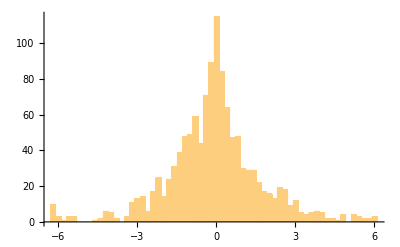

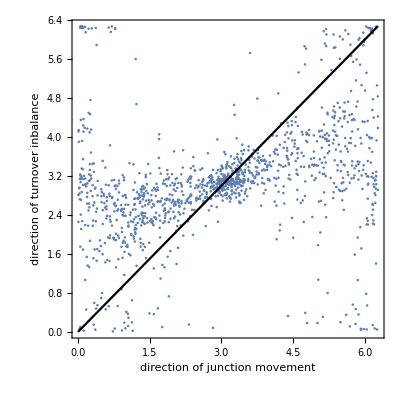

```mathematica
junctionVelocity[sim->1]=Flatten[
Table[
Table[Block[{
dirs1=pairs[[1,2,{3,4,5}]],
dirs2=pairs[[2,2,{3,4,5}]]
},

{
Mean[pairs[[All,1]]],(*average time between two time points*)
PlanarAngle[{0,0}->{{1,0},RotationMatrix[-Mean[{dirs1[[-1]],dirs2[[-1]]}]].(pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]])}],(*angular direction of movement*)
PlanarAngle[{0,0}->{{1,0},Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore,σInt.({Cos[#],Sin[#]}&/@(dirs2-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore}]}],(*angular direction of turnover mismatch*)
Norm[Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore,σInt.({Cos[#],Sin[#]}&/@(dirs2-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore}]],(*amplitude of turnover mismatch*)
Norm[pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]]](*distance junction moved*)
}],
{pairs,Partition[juncTrack,2]}],(*divide track into pairs of time points*)
{juncTrack,junctionTracks1}(*apply independently for each track*)],
1];
Histogram[((#[[2]]-#[[3]]))&/@junctionVelocity[sim->1],{-2Pi,2Pi,0.2}]
Show[ListPlot[(*Select[*)junctionVelocity[sim->1](*,#[[1]]>=times[[100]]&]*)[[All,{2,3}]],
AspectRatio->1,
Axes->None,Frame->True,FrameLabel->{"direction of junction movement","direction of turnover inbalance"}],
Plot[x,{x,0,2Pi},PlotStyle->Black]
]
```

The correlation for different directions isn’t good.
In the following, we do not include the core turnover.

### Analyze all simulations

#### Collect junction tracks in simulations 2 & 3

```mathematica
junctionTracks2={{tIni,#}}&/@(frameJunctions[sim->2][[1]]);
Do[Block[{
junctions=frameJunctions[sim->2][[i-indIni+1]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[junctionTracks2]],If[#[[-1,1]]==timePrev,Norm[junction[[{1,2}]]-#[[-1,2,{1,2}]]],Infinity]&/@junctionTracks2};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<5&&distancesSorted[[2,2]]>5,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[junctionTracks2[[distancesSorted[[1,1]]]],{time,junction}],
AppendTo[junctionTracks2,{{time,junction}}](*start a new track*)
];
,{junction,junctions}]
],{i,indIni+1,Length@times}];
```

```mathematica
junctionTracks3={{tIni,#}}&/@(frameJunctions[sim->3][[1]]);
Do[Block[{
junctions=frameJunctions[sim->3][[i-indIni+1]],
time=times[[i]],
timePrev=times[[i-1]],
distances,
distancesSorted
},
Do[
distances=Transpose@{Range[Length[junctionTracks3]],If[#[[-1,1]]==timePrev,Norm[junction[[{1,2}]]-#[[-1,2,{1,2}]]],Infinity]&/@junctionTracks3};
distancesSorted=SortBy[distances,#[[2]]&];
If[distancesSorted[[1,2]]<5&&distancesSorted[[2,2]]>5,(*ensure that only one junction from the previous time is close to the one we are looking at at the current time*)
AppendTo[junctionTracks3[[distancesSorted[[1,1]]]],{time,junction}],
AppendTo[junctionTracks3,{{time,junction}}](*start a new track*)
];
,{junction,junctions}]
],{i,indIni+1,Length@times}];
```

#### Analysis all simulations, both with and without core contribution

```mathematica
tCore0={0,0};
```

```mathematica
Do[
junctionVelocity0[sim->simInd]=Flatten[
Table[
Table[Block[{
dirs1=pairs[[1,2,{3,4,5}]],
dirs2=pairs[[2,2,{3,4,5}]]
},

{
Mean[pairs[[All,1]]],(*average time between two time points*)
PlanarAngle[{0,0}->{{1,0},RotationMatrix[-Mean[{dirs1[[-1]],dirs2[[-1]]}]].(pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]])}],(*angular direction of movement*)
PlanarAngle[{0,0}->{{1,0},Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore0,σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore0}]}],(*angular direction of turnover mismatch*)
Norm[Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore0,σInt.({Cos[#],Sin[#]}&/@(dirs2-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore0}]],(*amplitude of turnover mismatch*)
Norm[pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]]](*distance junction moved*)
}],
{pairs,Partition[juncTrack,2]}],(*divide track into pairs of time points*)
{juncTrack,Symbol["junctionTracks"<>ToString[simInd]]}(*apply independently for each track*)],
1];,
{simInd,3}];
```

```mathematica
Do[
junctionVelocity[sim->simInd]=Flatten[
Table[
Table[Block[{
dirs1=pairs[[1,2,{3,4,5}]],
dirs2=pairs[[2,2,{3,4,5}]]
},

{
Mean[pairs[[All,1]]],(*average time between two time points*)
PlanarAngle[{0,0}->{{1,0},RotationMatrix[-Mean[{dirs1[[-1]],dirs2[[-1]]}]].(pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]])}],(*angular direction of movement*)
PlanarAngle[{0,0}->{{1,0},Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore,σInt.({Cos[#],Sin[#]}&/@(dirs2-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore}]}],(*angular direction of turnover mismatch*)
Norm[Mean[{σInt.({Cos[#],Sin[#]}&/@(dirs1-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore,σInt.({Cos[#],Sin[#]}&/@(dirs2-Mean[{dirs1[[-1]],dirs2[[-1]]}]))-tCore}]],(*amplitude of turnover mismatch*)
Norm[pairs[[2,2,{1,2}]]-pairs[[1,2,{1,2}]]](*distance junction moved*)
}],
{pairs,Partition[juncTrack,2]}],(*divide track into pairs of time points*)
{juncTrack,Symbol["junctionTracks"<>ToString[simInd]]}(*apply independently for each track*)],
1];,
{simInd,2,3}]
```

#### Predict direction of movement

Make statistics of all junctions for times t>=100

Including core contribution

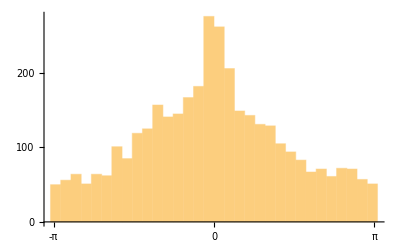

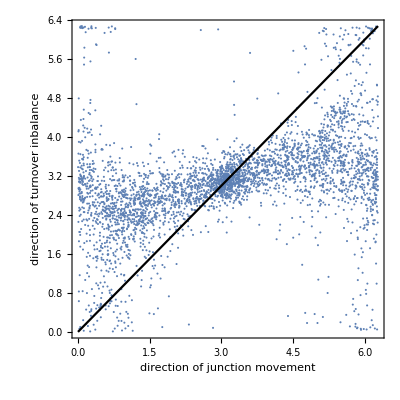

```mathematica
angleMismatch=(If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&@(#[[2]]-#[[3]]))&/@DeleteCases[Select[Join[junctionVelocity[sim->1],junctionVelocity[sim->2],junctionVelocity[sim->3]],#[[1]]>=times[[102]]&],{_,Indeterminate,_}];
Histogram[angleMismatch,{-3.2,3.2,0.2},Ticks->{{-Pi,0,Pi},{0,100,200}}]
Show[ListPlot[Select[Join[junctionVelocity[sim->1],junctionVelocity[sim->2],junctionVelocity[sim->3]],#[[1]]>=times[[102]]&][[All,{2,3}]],
AspectRatio->1,
Axes->None,Frame->True,FrameLabel->{"direction of junction movement","direction of turnover inbalance"}],
Plot[x,{x,0,2Pi},PlotStyle->Black]
]
```

Without core contribution

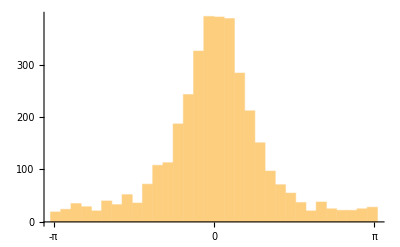

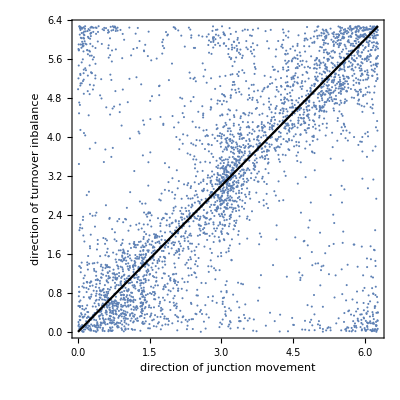

```mathematica
angleMismatch0=(If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&@(#[[2]]-#[[3]]))&/@DeleteCases[Select[Join[junctionVelocity0[sim->1],junctionVelocity0[sim->2],junctionVelocity0[sim->3]],#[[1]]>=times[[102]]&],{_,Indeterminate,_}];
Histogram[angleMismatch0,{-3.2,3.2,0.2},Ticks->{{-Pi,0,Pi},{0,100,200,300}}]
Show[ListPlot[Select[Join[junctionVelocity0[sim->1],junctionVelocity0[sim->2],junctionVelocity0[sim->3]],#[[1]]>=times[[102]]&][[All,{2,3}]],
AspectRatio->1,
Axes->None,Frame->True,FrameLabel->{"direction of junction movement","direction of turnover inbalance"}],
Plot[x,{x,0,2Pi},PlotStyle->Black]
]
```

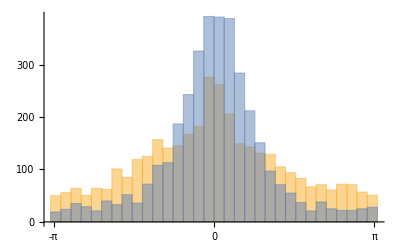

```mathematica
Histogram[{angleMismatch,angleMismatch0},{-3.2,3.2,0.2},Ticks->{{-Pi,0,Pi},{0,100,200,300,400}}]
```

```mathematica
Mean@Select[angleMismatch0,NumericQ]*180/Pi
StandardDeviation@Select[angleMismatch0,NumericQ]*180/Pi
```

0.613739

59.8241

### Scaling of the average pattern wavelength from junction density (simulation domain too small to reach scaling region)

```mathematica
wavelengths=Table[{times[[i]],Sqrt[30^2/Length[frameJunctions[sim->1][[i-indIni+1]]]],Sqrt[30^2/Length[frameJunctions[sim->2][[i-indIni+1]]]],Sqrt[30^2/Length[frameJunctions[sim->3][[i-indIni+1]]]]},
{i,indIni,Length@times}];
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
wavelength={#[[1]],Mean[#[[2;;]]]}&/@wavelengths;
```

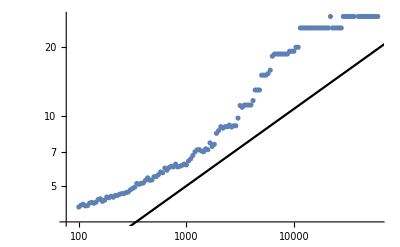

```mathematica
Show[
ListLogLogPlot[wavelength],
LogLogPlot[(t)^(1/3)/2,{t,1,10^5},PlotStyle->Black]
]
```